```mathematica
Subscript[k, 0]=20;
Subscript[X, 0]=-5;
Subscript[X, d]=-3;
δ=0.5;
Subscript[δ, 1]=0.005;

n=4;
m=20;
Ti=-0.02;
Tf=0.22;
dt=(Tf-Ti)/(m-1);

tm[0]=Ti-dt;
tm[1]=Ti;
tm[m+1]=Tf+dt;

Do[tm[i]=tm[i-1]+dt,{i,2,m}]

ψ[0,x_,t_]:=(δ^2/(2π))^(1/4)*Exp[-Subscript[k, 0]^2*δ^2]/(√(δ^2+(ⅈ*t)/2))*Exp[((2*δ^2* Subscript[k, 0] + ⅈ*(x-Subscript[X, 0]))^2)/(4*δ^2 + 2*ⅈ*t)]
K[xf_,tf_,xi_,ti_]:=1/(√(2*π*ⅈ*(tf-ti)))*Exp[(ⅈ*(xf-xi)^2)/(2*(tf-ti))]

a[1]=Abs[ψ[0,Subscript[X, d],Tm[1]]]*Sqrt[Subscript[δ, 1]];
b[1]=√(1-(a[1])^2);

Do[α[0,j]=ψ[0,Subscript[X, d],Tm[j]],{j,1,n+1}]

Do[Do[β[i,j]=K[Subscript[X, d],0,Subscript[X, d],Tm[j]-Tm[i]],{j,i+1,n+1}],{i,1,n}]

Do[Do[α[i,j]=(α[i-1,j]-α[i-1,i]*β[i,j]*Subscript[δ, 1])/b[i],{j,i+1,n+1}];a[i+1]=Abs[α[i,i+1]]*Sqrt[Subscript[δ, 1]];b[i+1]=√(1-(a[i+1])^2),{i,1,n}]
```

```mathematica
list={};Do[list=Append[list,tm[i]],{i,1,m}];TList=Permutations[list,{n}];
```

```mathematica
Length[TList]
```

0

```mathematica
TList[[5000]][[1]]
```

-0.02

```mathematica
TList[[7000]]
```

{0.0333333,0.06,0.193333,0.14,0.113333}

```mathematica
Do[Tm[j]=TList[[14000]][[j]],{j,1,n}]
```

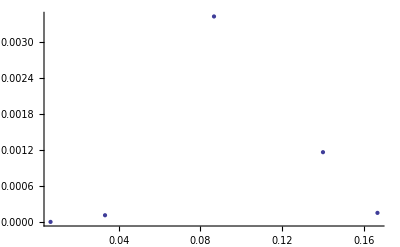

0.100713

```mathematica
ListPlot[Table[{Tm[i],(a[i])^2},{i,n}],PlotRange->All]
top=(∑_(j=1)^n Tm[j]*(Abs[α[0,j]])^2*Subscript[δ, 1])/(∑_(j=1)^n (Abs[α[0,j]])^2*Subscript[δ, 1])
```

```mathematica
Do[{Do[Tm[j]=TList[[i]][[j]],{j,1,n}]; Do[prob[i,j]=(∏_(k=1)^(j-1) b[k]^2)*(a[j])^2,{j,2,n,1}];
prob[i,1]=(a[1])^2  },{i,1,Length[TList]}]
```

```mathematica
prob[5040,3]
```

0.00380109

```mathematica
tbar=(∑_(i=1)^Length[TList] ∑_(j=1)^n (TList[[i]][[j]]*prob[i,j]))/(∑_(i=1)^Length[TList] ∑_(j=1)^n prob[i,j])
```

0.100508

```mathematica
.1-%
```

-0.000507727

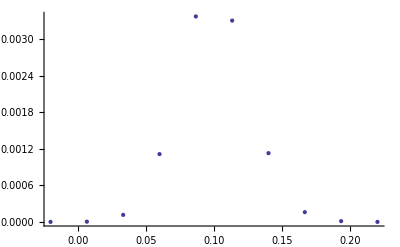

```mathematica
Do[prob[i_]:=(∏_(k=1)^(i-1) b[k]^2)*(a[i])^2,{i,2,n,1}]
prob[1]=(a[1])^2;

ListPlot[Table[{tm[i],prob[i]},{i,n}],PlotRange->All]

tbar=(∑_(j=1)^n (tm[j]*prob[j]))/(∑_(j=1)^n prob[j])
```